```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy485-optics

```mathematica
(*y = Sqrt[m ω/hbar ] x *)

psi0[y_] = E^( -y^2/2)
psi1[y_] = y E^(-y^2/2) /2
psi2[y_] = (4 y^2 - 2) E^(-y^2/2) /8
```

ⅇ^(-y^2/2)

1/2 ⅇ^(-y^2/2) y

1/8 ⅇ^(-y^2/2) (-2+4 y^2)

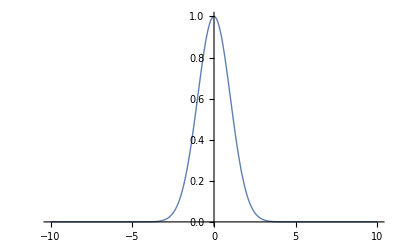

```mathematica
modernOpticsLecture18Fig3u0 = Plot[{psi0[y](*, Abs[psi0[y]]*)}, {y, -10, 10}, 
PlotStyle->Thick,
PlotRange ->Full]
```

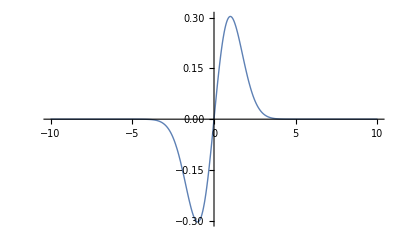

```mathematica
modernOpticsLecture18Fig3u1 =Plot[{psi1[y](*, Abs[psi1[y]]*)}, {y, -10, 10}, 
PlotStyle->Thick,
PlotRange ->Full]
```

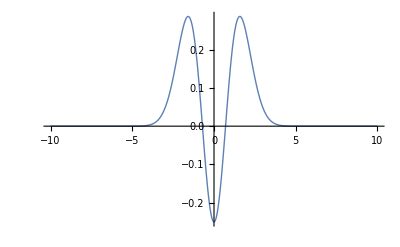

```mathematica
modernOpticsLecture18Fig3u2 = Plot[{psi2[y](*, Abs[psi2[y]]*)}, {y, -10, 10}, 
PlotStyle->Thick,
PlotRange ->Full]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture18Fig3u0",modernOpticsLecture18Fig3u0]
peeters`exportForLatex["modernOpticsLecture18Fig3u1",modernOpticsLecture18Fig3u1]
peeters`exportForLatex["modernOpticsLecture18Fig3u2",modernOpticsLecture18Fig3u2]
```

{modernOpticsLecture18Fig3u0.eps,modernOpticsLecture18Fig3u0pn.png}

{modernOpticsLecture18Fig3u1.eps,modernOpticsLecture18Fig3u1pn.png}

{modernOpticsLecture18Fig3u2.eps,modernOpticsLecture18Fig3u2pn.png}